```mathematica
vertexNumber = Reverse[{33288,16859, 12802, 10195, 5673, 3728, 2069, 906, 399, 303, 278}];
distanceErrors = Reverse[{-0.000669728,-0.000300969,  -0.000121638, -2.39167 E^(-05), 0.000312029, 0.000477913, 0.000810055, 0.00114282, 0.00367975, 0.00327267, 0.003672}];
averageOverlaps = Reverse[{0.999784,0.999859, 0.999831, 0.999711, 0.999645,0.99956 , 0.999409, 0.998657, 0.993277, 0.997023, 0.99623}];
averageTimes = Reverse[{8.91615,2.6437, 1.49639, 0.953703, 0.324324, 0.154851, 0.056301, 0.0138335, 0.00508005, 0.00338657, 0.002598}];
logVertexNumber = Table[N[Log[vertexNumber[[i]]]],{i,Length[vertexNumber]}]
logDistanceError = Table[N[Log[distanceErrors[[i]]]],{i,Length[vertexNumber]}]
logOverlaps = Table[N[Log[averageOverlaps[[i]]]],{i,Length[vertexNumber]}]
logTimes = Table[N[Log[averageTimes[[i]]]],{i,Length[vertexNumber]}]
```

{5.62762,5.71373,5.98896,6.80904,7.63482,8.22363,8.64347,9.22965,9.45736,9.73264,10.413}

{-5.60702,-5.72215,-5.60491,-6.77426,-7.11841,-7.64608,-8.07241,-4.12801+3.14159 ⅈ,-9.01446+3.14159 ⅈ,-8.1085+3.14159 ⅈ,-7.30864+3.14159 ⅈ}

{-0.00377712,-0.00298144,-0.0067457,-0.0013439,-0.000591175,-0.000440097,-0.000355063,-0.000289042,-0.000169014,-0.00014101,-0.000216023}

{-5.95301,-5.68794,-5.28243,-4.28066,-2.87704,-1.86529,-1.12601,-0.047403,0.403056,0.972179,2.18786}

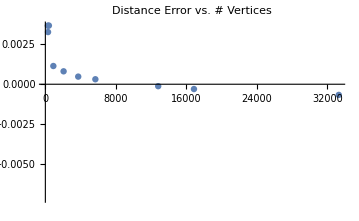

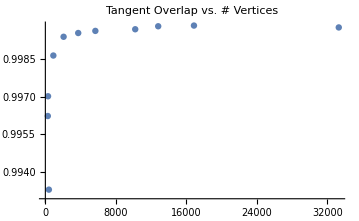

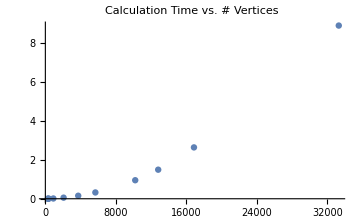

----

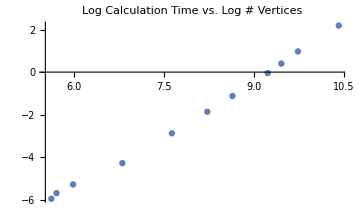

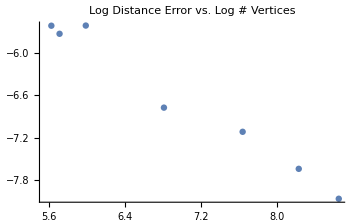

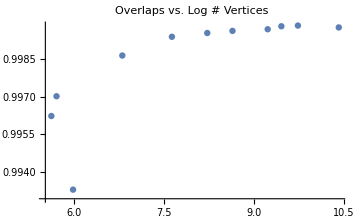

```mathematica
distErrorVsVertexNumber =Transpose@{vertexNumber,distanceErrors};
overlapsVsVertexNumber =Transpose@{vertexNumber,averageOverlaps};
timesVsVertexNumber =Transpose@{vertexNumber,averageTimes};
LogTimesVsLogVertexNumber =Transpose@{logVertexNumber,logTimes};
LogDistancesVsLogVertexNumber =Transpose@{logVertexNumber,logDistanceError};
OverlapsVsLogVertexNumber = Transpose@{logVertexNumber,averageOverlaps};
ListPlot[distErrorVsVertexNumber,PlotLabel->"Distance Error vs. # Vertices"]
ListPlot[overlapsVsVertexNumber, PlotLabel->"Tangent Overlap vs. # Vertices"]
ListPlot[timesVsVertexNumber, PlotLabel->"Calculation Time vs. # Vertices"]
Print["----"]
ListPlot[LogTimesVsLogVertexNumber, PlotLabel->"Log Calculation Time vs. Log # Vertices"]
ListPlot[LogDistancesVsLogVertexNumber, PlotLabel->"Log Distance Error vs. Log # Vertices"]
ListPlot[OverlapsVsLogVertexNumber, PlotLabel->"Overlaps vs. Log # Vertices"]
```

FittedModel[0.5+0.5/(1+ⅇ^(-0.656298-«19» x))]

0.999999

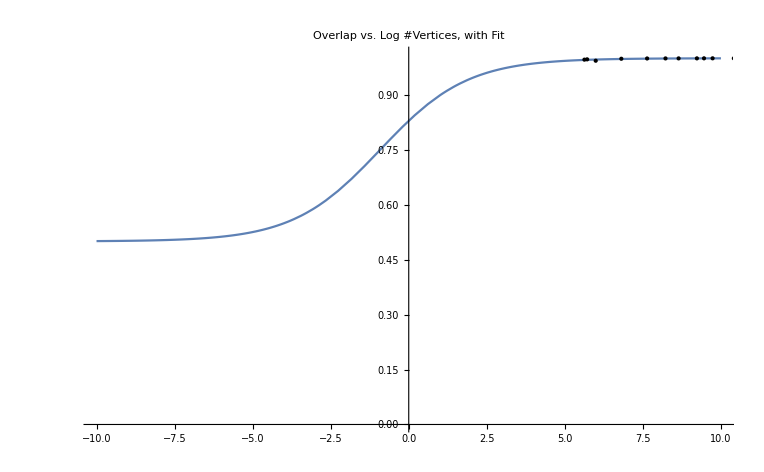

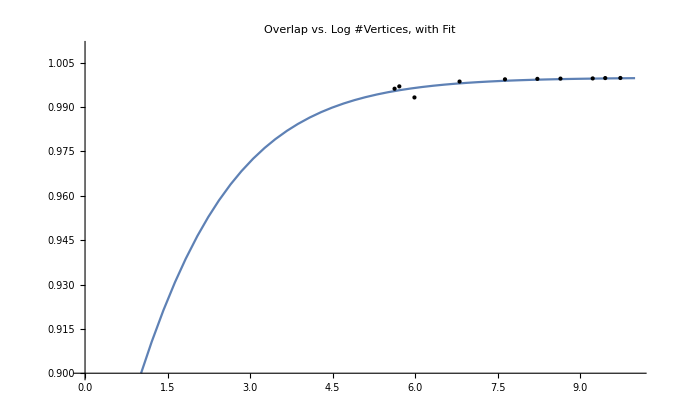

```mathematica
overlapModel =.5+(.5)/(1+ⅇ^(-b*x+a));
overlapLogFit = NonlinearModelFit[OverlapsVsLogVertexNumber,overlapModel,{a,b},x]
overlapLogFit["RSquared"]
Plot[overlapLogFit[x],{x,-10,10},Epilog->Map[Point,OverlapsVsLogVertexNumber],PlotRange->{0,1.01},PlotLabel->"Overlap vs. Log #Vertices, with Fit"]
```

FittedModel[-15.4509+1.67368 x]

R^2=

0.997919

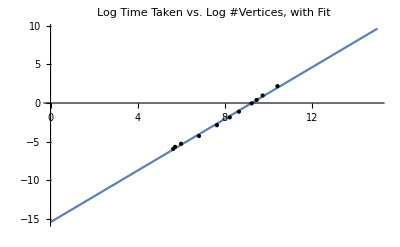

```mathematica
timeModel =a*x+b;
timeLogFit =NonlinearModelFit[LogTimesVsLogVertexNumber,timeModel,{a,b},x]
Print["R^2="];timeLogFit["RSquared"]
Plot[timeLogFit[x],{x,0,15},Epilog->Map[Point,LogTimesVsLogVertexNumber],PlotRange->All,PlotLabel->"Log Time Taken vs. Log #Vertices, with Fit"]
```

```mathematica
distErrorVsVertexNumber
```

{{399,0.00367975},{906,0.00114282},{2069,0.000810055},{3728,0.000477913},{5673,0.000312029},{10195,-0.0161149},{12802,-0.000121638},{16859,-0.000300969},{33288,-0.000669728}}

-0.000669728+x^b

FittedModel[-0.000669728+1/x^0.957087]

R^2=0.17878

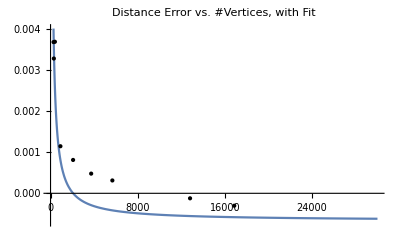

```mathematica
distModel =x^(b)-0.000669728
distFit =NonlinearModelFit[distErrorVsVertexNumber,distModel,{a,b,c},x]
Print["R^2=",distFit["RSquared"]];
Plot[distFit[x],{x,0,30000},Epilog->Map[Point,distErrorVsVertexNumber],PlotRange->{-0.0007,.004},PlotLabel->"Distance Error vs. #Vertices, with Fit"]
```